The file format for the file is a list of points with seven entries each. The entries contain the following:

1) {x, y}, the parameter values over which the loop was iterated

2) {M1, M2, M3, M0, Mtau, 
MQ, MNR, tanβ, v, vevS, 
Atop, Abtm, Atau, An11, An12,
 An13, AlambdaN, Yn11, Yn12, Yn13, 
 lambda, lambdaN, kappa, PhisPI, Phi2PI, 
 ksi, Alambda, Akappa}, the input parameters
 
3) {χN-mass(5),  χC-mass(2), H+-mass(2), ν-mass(4), snu-mass(8), 
H0-mass(6), slep-mass(6), sup-mass(2), sdn-mass(2), stp-mass(2), 
sbt-mass(2)}, the mass eigenvalues, each of these is a vector in itself with the dimension noted in parentheses.

4) {χNre(5x5), χNim(5x5), 
χC-Ure(2x2),  χCU-im(2x2), χCV-re(2x2), χCV-im(2x2),  
νre(4x4), νim(4x4), 
H0(6x6), 
snu(8x8), 
slepCre(6x6), slepCim(6x6), 
sdown-re(2x2), sdown-im(2x2), sup-re(2x2), sup-im(2x2), stop-re(2x2), stop-im(2x2), sbottom-re(2x2), sbottom-im(2x2),
H+-(2x2)}, the mixing matrices, each of these is a nxn matrix with the dimensions noted in parentheses

5) {contribution in %, absolute contribution, channel}, the contributing channels to omega

6) {omega, CDM candidate name, Xf}, self explanatory

7) {cross section in pb, input channel, output channel}, cross sections for selected channels

8) CDM nucleon magic (amp = micromegas Amplitude, cs=cross section [pb])
{{n-cdm SI amp, n-anti-cdm SI amp, n-cdm SD amp, n-anti-cdm SD amp}, 
  {p-cdm SI amp, p-anti-cdm SI amp, p-cdm SD amp, p-anti-cdm SD amp}, 
  {n-cdm SI cs, n-anti-cdm SI cs, n-cdm SD cs, n-anti-cdm SD cs}, 
  {p-cdm SI cs, p-anti-cdm SI cs, p-cdm SD cs, p-anti-cdm SD cs}}

 9) Bsgamma ect
 
 10) {{Δa_e, Δa_μ, Δa_τ},
 {d_e, d_μ, d_τ}, 
 {BR( τ -> μ γ ), BR( τ -> e γ ), BR( μ -> e γ ) }}

```mathematica
file4=<<"/Users/ruppell/Math/temp/output-cpx-joined-edm_clean.txt";
```

```mathematica
file100=<<"/Users/ruppell/Math/temp/output-cpc-edm_clean.txt";
```

```mathematica
file101=<<"/Users/ruppell/Math/temp/output-cpc-new.txt";
```

```mathematica
Dimensions@file4
```

{3312,10}

```mathematica
file10=<<"/Users/ruppell/Math/temp/output-cpx-higgs-phase-edm_clean3.txt";
file20=<<"/Users/ruppell/Math/temp/output-cpx-higgs-edm_clean.txt";
```

```mathematica
snuLSP[name_]:=Select[name,#[[3,5,1]]<Abs@#[[3,1,1]]&];
χ0LSP[name_]:=Select[name,#[[3,5,1]]>Abs@#[[3,1,1]]&];
χ0sing[name_]:=Select[name,Power[Abs@(#[[4,1,1,5]]+I #[[4,2,1,5]]),2]>0.1&];
χ0doub[name_]:=Select[name,Power[Abs@(#[[4,1,1,5]]+I #[[4,2,1,5]]),2]<0.1&];
snuLeft[name_]:=Select[name,#[[4,10,1,4]]^2+#[[4,10,1,8]]^2<0.99&];
snuRight[name_]:=Select[name,#[[4,10,1,4]]^2+#[[4,10,1,8]]^2>0.99&];
bsg[name_]:=Select[name,(#[[9,1]]<4.97*^-4&&#[[9,1]]>2.13*^-4)&];
ΔMd[name_]:=Select[name,(#[[9,2]]<5.15*^-1&&#[[9,2]]>4.99*^-1)&];
ΔMs[name_]:=Select[name,(#[[9,3]]<1.753*^1&&#[[9,3]]>1.801*^1)&];
bsμμ[name_]:=Select[name,(#[[9,4]]<4.5*^-9)&];
bτν[name_]:=Select[name,(#[[9,5]]<2.45*^-4&&#[[9,5]]>8.9*^-5)&];
dϵ[name_]:=Select[name,(#[[10,2,1]]<1.43*^-27&&#[[10,2,1]]>-0.5*^-28)&];
dμ[name_]:=Select[name,(#[[10,2,2]]<0.8*^-19)&];
BRτμγ[name_]:=Select[name,(#[[10,3,1]]<4.4*^-8)&];
BRτϵγ[name_]:=Select[name,(#[[10,3,2]]<3.3*^-8)&];
BRμϵγ[name_]:=Select[name,(#[[10,3,3]]<1.2*^-11)&];
selSnuMass[down_,up_][name_]:=Select[name,(#[[3,5,1]]<up&&#[[3,5,1]]>down)&];
selHiggsMass[down_,up_][name_]:=Select[name,Or@@((#<up&&#>down)&/@#[[3,6,{2,3,4,5,6}]])&];
```

```mathematica
cuts=BRμϵγ@BRτϵγ@BRτμγ@dμ@dϵ@bτν@bsμμ@bsg@#&;
h1[name_]:=Select[name,(#[[3,6,2]]<128&&#[[3,6,2]]>123)&];
h23[name_]:=Select[name,((#[[3,6,3]]<128&&#[[3,6,3]]>123)||(#[[3,6,4]]<128&&#[[3,6,4]]>123))&];
h123[name_]:=Select[name,((#[[3,6,2]]<128&&#[[3,6,2]]>123)||(#[[3,6,3]]<128&&#[[3,6,3]]>123)||(#[[3,6,4]]<128&&#[[3,6,4]]>123))&];
dm[name_]:=Select[name,(#[[6,1]]<0.1311&&#[[6,1]]>0.0941)&];
dmup[limU_,limD_][name_]:=Select[name,(#[[6,1]]<limU&&#[[6,1]]>limD)&];
```

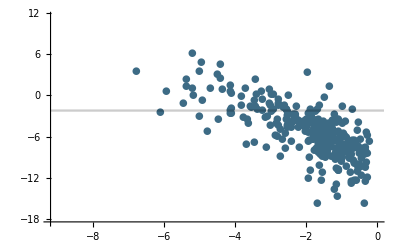

```mathematica
p2=ListLogLogPlot[
{Transpose@{(snuRight@snuLSP@file20)[[;;,2,22]],(snuRight@snuLSP@file20)[[;;,6,1]]},
Transpose@{(snuRight@snuLSP@file10)[[;;,2,22]],(snuRight@snuLSP@file10)[[;;,6,1]]},
Transpose@{(snuLeft@snuLSP@file20)[[;;,2,22]],(snuLeft@snuLSP@file20)[[;;,6,1]]}
},
ImageSize->400,
PlotRange->{{10^-4,1},{10^-8,100000}},
PlotStyle->ColorData[31,"ColorList"][[{9,9,5}]],
PlotMarkers->{{●,10},{●,10},{▲,10}},
TicksStyle->Medium,
Epilog->{Opacity[0.2,Black],Rectangle[{Log@(10^-4),Log@0.1311},{1,Log@0.0941}]}]
```

```mathematica
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/RDvsLamNPlot.eps",p2,"EPS"]
```

/Users/ruppell/Documents/Latex/papers/ScalarDM/RDvsLamNPlot.eps

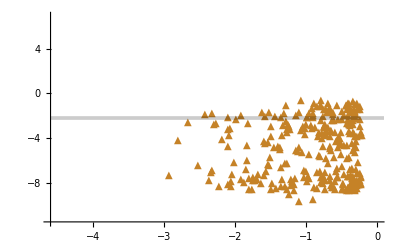

```mathematica
p2=ListLogLogPlot[
{Transpose@{Abs@(χ0doub@χ0LSP@file10)[[;;,2,23]],(χ0doub@χ0LSP@file10)[[;;,6,1]]},
Transpose@{Abs@(χ0sing@χ0LSP@file10)[[;;,2,23]],(χ0sing@χ0LSP@file10)[[;;,6,1]]}
},
ImageSize->400,
PlotStyle->ColorData[31,"ColorList"][[{5,9}]],
PlotMarkers->{{▲,10},{●,10}},
PlotRange->{{10^-2,1},{10^-5,1000}},
TicksStyle->Medium,
Epilog->{Opacity[0.2,Black],Rectangle[{Log@(10^-2),Log@0.1311},{1,Log@0.0941}]}]
```

```mathematica
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/RDvsKapPlot.eps",p2,"EPS"]
```

/Users/ruppell/Documents/Latex/papers/ScalarDM/RDvsKapPlot.eps

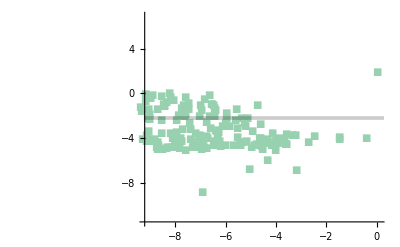

```mathematica
p4=ListLogLogPlot[
{Transpose@{Power[Abs@((χ0LSP@file100)[[1000;;2000,4,1,1,5]]+I(χ0LSP@file100)[[1000;;2000,4,2,1,5]]),2],Abs@(χ0LSP@file100)[[1000;;2000,6,1]]},
Transpose@{Power[Abs@((χ0doub@χ0LSP@file10)[[;;,4,1,1,5]]+I(χ0doub@χ0LSP@file10)[[;;,4,2,1,5]]),2],Abs@(χ0doub@χ0LSP@file10)[[;;,6,1]]},
Transpose@{Power[Abs@((χ0sing@χ0LSP@file10)[[;;,4,1,1,5]]+I(χ0sing@χ0LSP@file10)[[;;,4,2,1,5]]),2],Abs@(χ0sing@χ0LSP@file10)[[;;,6,1]]}
},
ImageSize->400,
PlotStyle->ColorData[31,"ColorList"][[{7,5,9}]],
PlotMarkers->{{■,10},{▲,10},{●,10}},
PlotRange->{{10^-4,1.1},{10^-5,1000}},
TicksStyle->Medium,
Epilog->{Opacity[0.2,Black],Rectangle[{Log@(10^-4),Log@0.1311},{1,Log@0.0941}]}]
```

```mathematica
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/RDvsScomp.eps",p4,"EPS"]
```

/Users/ruppell/Documents/Latex/papers/ScalarDM/RDvsScomp.eps

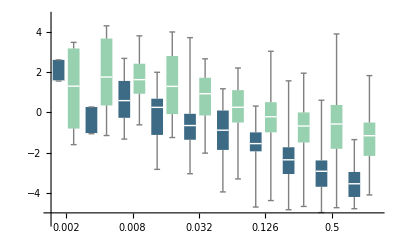

```mathematica
p5=BoxWhiskerChart[Transpose@{Flatten[BinLists[Transpose@{10~Log~(snuRight@snuLSP@file20)[[;;,2,22]],10~Log~(snuRight@snuLSP@file20)[[;;,6,1]]},{-3,0,0.3},{-5,5,10}][[;;,;;,;;,2]],1],
Flatten[BinLists[Transpose@{10~Log~(snuRight@snuLSP@file100)[[;;,2,22]],10~Log~(snuRight@snuLSP@file100)[[;;,6,1]]},{-3,0,0.3},{-5,5,10}][[;;,;;,;;,2]],1]},
ChartStyle->ColorData[31,"ColorList"][[{9,7}]],
Frame->None,
Axes->True,
AxesOrigin->{0.5,-5},
Ticks->{{{1.5,0.002},{3.7,0.004},{5.9,0.008},{8.1,0.016},{10.3,0.032},{12.5,0.063},{14.700000000000001,0.126},{16.900000000000002,0.25},{19.1,0.5},{21.3,1}},Automatic}
]
```

```mathematica
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/RsnuCPCvsCPXplot.eps",p5,"EPS"]
```

/Users/ruppell/Documents/Latex/papers/ScalarDM/RsnuCPCvsCPXplot.eps

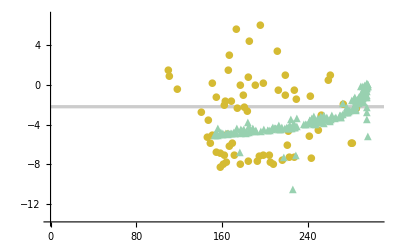

```mathematica
p2=ListLogPlot[
{Transpose@{Abs@(χ0sing@χ0LSP@file4[[;;1000]])[[;;,3,1,1]],(χ0sing@χ0LSP@file4[[;;1000]])[[;;,6,1]]},
Transpose@{Abs@(χ0doub@χ0LSP@file100[[;;1000]])[[;;,3,1,1]],(χ0doub@χ0LSP@file100[[;;1000]])[[;;,6,1]]},Transpose@{Abs@(χ0doub@χ0LSP@file4[[;;1000]])[[;;,3,1,1]],(χ0doub@χ0LSP@file4[[;;1000]])[[;;,6,1]]},
Transpose@{Abs@(χ0sing@χ0LSP@cuts@file4[[;;2000]])[[;;,3,1,1]],(χ0sing@χ0LSP@cuts@file4[[;;2000]])[[;;,6,1]]},
Transpose@{Abs@(χ0doub@χ0LSP@cuts@file4[[;;1000]])[[;;,3,1,1]],(χ0doub@χ0LSP@cuts@file4[[;;1000]])[[;;,6,1]]},
{{286.3,3.3*10^-3},
{276.7,8.3*10^-4},
{196.6,6.5*10^-4}}
},
ImageSize->400,
PlotRange->{{0,305},{0.000001,1000}},
PlotStyle->ColorData[31,"ColorList"][[{6,7,5,3,3,3}]],
PlotMarkers->{{●,10},{▲,10},{▲,10},{●,17},{▲,17},{▲,17}},
TicksStyle->Medium,
Prolog->{Opacity[0.2,Black],Rectangle[{0,Log@0.1311},{500,Log@0.0941}]}]
```

```mathematica
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/RDvsChi0mass.eps",p2,"EPS"]
```

/Users/ruppell/Documents/Latex/papers/ScalarDM/RDvsChi0mass.eps

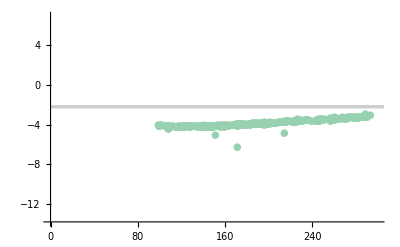

```mathematica
p2=ListLogPlot[
{Transpose@{(snuLeft@snuLSP@file100[[;;1000]])[[;;,3,5,1]],(snuLeft@snuLSP@file100[[;;1000]])[[;;,6,1]]},Transpose@{(snuRight@snuLSP@file4[[;;1000]])[[;;,3,5,1]],(snuRight@snuLSP@file4[[;;1000]])[[;;,6,1]]},Transpose@{(snuLeft@snuLSP@file4[[;;1000]])[[;;,3,5,1]],(snuLeft@snuLSP@file4[[;;1000]])[[;;,6,1]]},
Transpose@{(snuLeft@snuLSP@file20[[;;500]])[[;;,3,5,1]],(snuLeft@snuLSP@file20[[;;500]])[[;;,6,1]]},Transpose@{(snuLSP@cuts@file4[[;;1000]])[[;;,3,5,1]],(snuLSP@cuts@file4[[;;1000]])[[;;,6,1]]},
{{183.7,2.9*10^-4}}
},
ImageSize->400,
PlotRange->{{0,300},{0.000001,1000}},
PlotStyle->ColorData[31,"ColorList"][[{7,6,5,5,3,3,3}]],
PlotMarkers->{{●,10},{▲,10},{●,10},{●,10},{▲,17},{▲,17},{▲,17}},
TicksStyle->Medium,
Prolog->{Opacity[0.2,Black],Rectangle[{0,Log@0.1311},{500,Log@0.0941}]}]
```

```mathematica
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/RDvsSnumass.eps",p2,"EPS"]
```

/Users/ruppell/Documents/Latex/papers/ScalarDM/RDvsSnumass.eps